```mathematica
<<prism`
```

```mathematica
Manipulate[
s[
glass[θ,n],
internalRay0[θ,n],

sourceRay[θ,n],
sourceRay2[θ,n],
(*sourceRay3[θ,n],*)

(*ray1[θ,n],
ray2[θ,n],
ray3[θ,n],
ray4[θ,n],
ray5[θ,n],
ray6[θ,n],*)

txtDelta[θ,n],
txtN[θ,n],
txtThetaI1[θ,n],
txtThetaT2[θ,n]
]


,{{n,1.76},1.001,2,0.01},{θ,(55π)/200,π/2,π/200}]
```

## minDev from n

-Graphics-

```mathematica
nr=Rationalize[1.76];
α=π/3;

δ[θi1_]:=θi1+ArcSin[(Sin[α])√(nr^2-Sin[θi1]^2)-Sin[θi1]Cos[α]]-α;
extract=N[Quiet[#]⟦1,1⟧⟦2⟧]& ;
minimumDeviation=δ[extract[Solve[D[δ[θ],θ]==0]]//N]//r2D
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

63.2847

## n from minDev

```mathematica
refIndex[minDev_]:=Sin[(minDev+π/3)/2]/Sin[π/3/2] ;
N[refIndex[d2R[63]]]
```

2. Sin[0.5 (1.0472+d2R[63.])]

## tools

```mathematica
r2D=(180.0/π)#&;
d2R=(180/π)^-1#&;
```

## Plotting Deviation Curve

-Graphics-

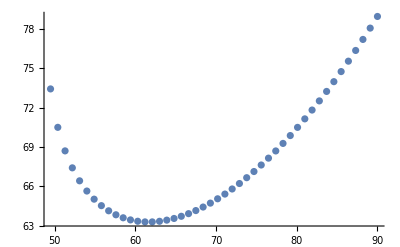

```mathematica
nr=Rationalize[1.76];
α=π/3;

δ[θi1_]:=θi1+ArcSin[(Sin[α])√(nr^2-Sin[θi1]^2)-Sin[θi1]Cos[α]]-α;
format=(ToString[AccountingForm[#,2]]<>"°")&;
deltaVector=r2D/@(δ/@(Range[(53π)/200,π/2,π/200]));
thetaVector=r2D/@(Range[(53π)/200,π/2,π/200]);
ListPlot[Transpose[{thetaVector,deltaVector}]]
```